## Unit Square N_s=162 μ_a=log(3)=1.09861 μ_s=2log(2)=1.38629 g=0.5

The specific intensity for a triangle centered at (0.63,0.71)
	RULE1		# of point	degree of exactness
	1		7		5
	2		25		10
	3		54		15
	4		84		20
	5		126		25
	6		175		30

### New L2 Error

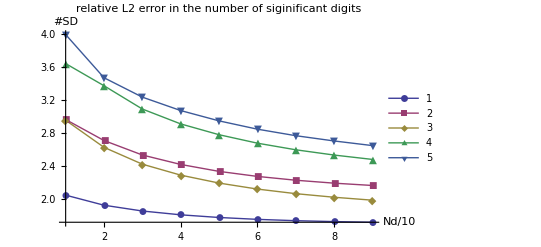

Below are the explanation copied from a previous email:

The source integral in both the impedance matrix and the right hand side upon first-order extraction can be computed to machine precision. However, the testing integrals are much more difficult to compute accurately. Even with RULE1=6, i.e., 175-pt quadrature rule on testing integrals, the testing integrals only converge to 2~3 digits (with justifications that are not essential for now). The source of this difficulty might be due to the highly oscillatory integrand that varies as exp[-i m phi] where m could be as high as Nd. The higher Nd is, the less accurately the testing integrals can be computed using the same quadrature rules. With increasing Nd, the impedance matrix and the new right hand side are computed less and less accurately with the existing code. Therefore, it might be reasonable to think of the seemingly strange L2 error curves as due to the inability to compute the testing integrals with very high Nd (~100).

## Unit Square N_s=162 μ_a=log(2)=0.693147 μ_s=5log(2)=3.46574 g=0.9

The specific intensity for a triangle centered at (0.63,0.71)

### New L2 Error

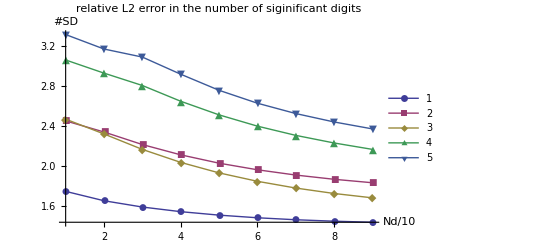

## Plotting Codes

#### Single plot

n=121

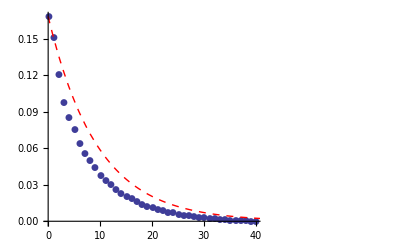

```mathematica
ClearAll[ndlist,raw1,data,RULE1]
RULE1=6;
ndlist=Range[10,90,10];
SetDirectory[NotebookDirectory[]];
raw1=Table[Partition[Import["solx2/sol"<>ToString[RULE1]<>"/162_"<>ToString[nd],"Complex128"],2 nd+1],{nd,ndlist}];
ResetDirectory[];
ClearAll[n]
n=121;
(*Print["RULE1=",RULE1];*)
Print["n=",n];
(data=Table[Table[{m,raw1[[i,n,m+ndlist[[i]]+1]]},{m,0,ndlist[[i]]}],{i,Length[ndlist]}]//Re)//ListLinePlot[#,PlotRange->{{10,20},{0.01,0.04}},PlotMarkers->Automatic,PlotLegends->ndlist]&;
raw1[[9,n]]//Re//ListPlot[#,PlotRange->Automatic]&;
Show[i=9;Table[{m,raw1[[i,n,m+ndlist[[i]]+1]]},{m,0,ndlist[[i]]}]//Re//ListPlot[#,PlotRange->{{0,40},All},PlotMarkers->Automatic]&,Plot[raw1[[i,n,ndlist[[i]]+1]] 0.9^( m),{m,0,90},PlotRange->All,PlotStyle->{Dashed,Thick,Red}]]
```

#### L2 error

```mathematica
ClearAll[ndlist,raw2,rule1range]
rule1range=Range[6];
ndlist=Range[10,90,10];
SetDirectory[NotebookDirectory[]];
raw2=Table[Table[Partition[Import["solx2/sol"<>ToString[RULE1]<>"/162_"<>ToString[nd],"Complex128"],2 nd+1]⟦All,nd+1;;2nd+1⟧//Chop,{nd,ndlist}],{RULE1,rule1range}];
ResetDirectory[];
```

```mathematica
raw2⟦6,9⟧//Dimensions;
norm2=ParallelSum[Abs[raw2⟦-1,-1,n,m⟧]^2,{m,1,ndlist⟦-1⟧+1},{n,1,162}];
data2=Table[Table[-Log[ParallelSum[Abs[raw2⟦RULE1,i,n,m⟧-raw2⟦-1,i,n,m⟧]^2,{m,1,ndlist⟦i⟧+1},{n,1,162}]/norm2]/Log[10]/2,{i,Length[ndlist]}],{RULE1,rule1range⟦1;;-2⟧}];
(*diffnormlist/normlist//ListLinePlot[#,PlotMarkers->Automatic,PlotLegends->Automatic]&*)
```

```mathematica
ListLinePlot[data2,PlotRange->{rule1range⟦1;;-2⟧,{0,All}},PlotMarkers->Automatic,PlotLegends->Automatic,AxesLabel->{"Nd/10","#SD"},PlotLabel->"relative L2 error in the\n number of siginificant digits"]
```

-Graphics-

#### Right Hand Side

```mathematica
ClearAll[rhs,RULE1,nd]
{RULE1,nd}={5,90};
n=20;
SetDirectory[NotebookDirectory[]];
rhs=Partition[Import["solx1/sol"<>ToString[RULE1]<>"/162_"<>ToString[nd]<>".rhs","Complex128"],2 nd+1]⟦All,nd+1;;2nd+1⟧//Chop;
ResetDirectory[];
```

```mathematica
{Table[{m,rhs[[n,m+1]]//Re},{m,0,nd}],Table[{m,rhs[[n,m+1]]//Im},{m,0,nd}]}//ListLinePlot[#,PlotRange->{{0,20},All},PlotMarkers->Automatic,PlotLegends->{"Re","Im"}]&
```